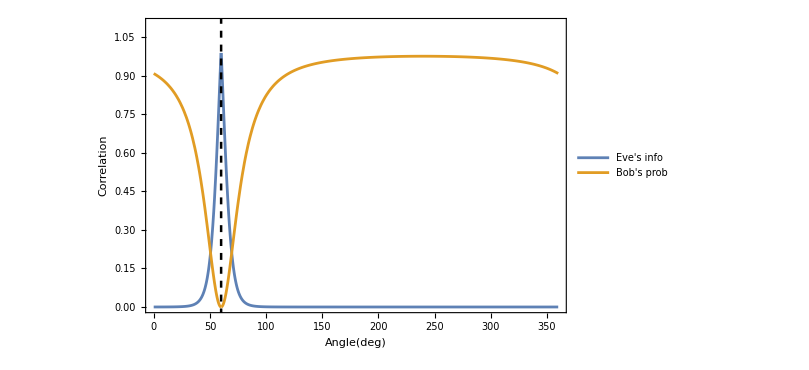

test2.jpg

```mathematica
(*Mathematica Code for Figure 6 in `CV QKD with Single Quadrature Measurement at Arbitrary Reference Frame'*)
VE:=1
θ1:=Pi/3
y1:=1/(2*Pi)(VE/Abs[Cos[Pi/2+(x  Degree-θ1)/2]])
y2:=2/Pi ArcTan[y1]
y3:=(y1^2/(1+y1^2))^2*y2^3
y5:=1-(y1^2/(1+y1^2))
test=With[{x0=60,tickf={#,StringJoin[ToString[#],"°"]}&},Plot[{y3,y5},{x,0,360},Frame->True,FrameLabel->{Angle  [deg],Correlation},LabelStyle->{Directive[Black,20]},PlotRange->{{0,360},{0,1.1}},PlotLegends->Placed[{"Eve's info","Bob's prob"},{Right,Bottom}],Ticks->{tickf/@FindDivisions[{0,360,45},8],Automatic},GridLines->{{x0},{}},GridLinesStyle->Directive[Black, Dashed,Thickness[0.003]]]]
Export["test2.jpg",test]
Int:=FullSimplify[Integrate[y1,{x,0,1}]]
```